```mathematica
<<MaTeX`
ClearAll[plotColors];
plotColors::usage="plotColors[plotType,plotTheme] gives a list of the colors used in a plot when several curves are drawn. Here plotType is, for example, Plot or ListLogPlot while plotTheme may be \"Scientific\", \"Classic\" etc.";
plotColors[plotType_,plotTheme_]:=("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme[plotTheme,plotType]))/.Directive[x_,__]:>x;
pltcolors=plotColors[ListLinePlot,"Scientific"];
```

## Parámetros

```mathematica
(*HNL DECAYS TOO MESONS/LEPTONS*)(*ESTE SCRIPT GENERA LOS ARCHIVOS PCONFIG QUE UTILIZA PYTHIA8.*)(*NOTAR QUE SIEMPRE TOMA COMO ARGUMENTO LA MASA DEL HNL*)e=0.5109989461*10^-3;
mu=105.6583745*10^-3;
tau=1.77686;
leptons={e,mu,tau};
tfactor=1.5193*10^24(*Para pasar de s a GeV^-1*);mmc=3*10^11(*para pasar de s a mm/c*);
ckm=({{0.9742,0.2243,0.0365},{0.218,0.997,0.0422},{0.0081,0.0394,1.019}});
gf=1.166378*10^-5;
xw=0.2223;
gll=-(1/2)+xw;
glr=xw;

(*charged pseudoscalar*)
(* 1.tau 2.m 3.f 4.CKM 5.id*)
d431={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],431};
d431bar={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],-431};
d411={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],411};
d411bar={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],-411};
k321={1.238*10^-8*tfactor,493.677*10^-3,155.6*10^-3,ckm[[1,2]],321};
pi211={2.6*10^-8*tfactor,139.57061*10^-3,130.2*10^-3,ckm[[1,1]],211};

d421={410.1*10^-15*tfactor,1.86483,Null,Null,421};
k311={Null,0.497611,Null,Null,311};
k313={Null,0.89555,Null,Null,313};

(*Charged vector*)
k323={Null,895.55*10^-3,0.1827,ckm[[1,2]],323}(*K*(892)*);
rho770c={Null,775.26*10^-3,0.162,ckm[[1,1]]};

(*neutral pseudoscalar*)
pi111={Null,134.977*10^-3,130.2*10^-3,Null,111};
eta221={Null,547.862*10^-3,81.7*10^-3,Null,221}(*eta*);
eta331={Null,957.78*10^-3,-94.7*10^-3,Null,331}(*eta prime*);
(*Neutral vector*)
rho770n={Null,775.26*10^-3,0.162,1-2xw};
omega782={Null,782.65*10^-3,0.153,4/3 xw};
phi1020={Null,1.019461,0.234,4/3 xw-1,333};

datae=Import[NotebookDirectory[]<>"/mainconfig/mixe.dat"];
datamu=Join[Table[{i,1},{i,0.01,0.1,0.01}],Import[NotebookDirectory[]<>"/mainconfig/mixmu.dat"]];
datatau=Import[NotebookDirectory[]<>"/mainconfig/mixtau.dat"];
fmixe=Interpolation[datae,InterpolationOrder->1];
fmixmu=Interpolation[datamu,InterpolationOrder->1];
fmixtau=Interpolation[datatau,InterpolationOrder->1];
```

## Leptonic decays (Shaposhnikov)

```mathematica
(***************MESON DECAY*******************)
(*meson decay BRs function*)
width2body[meson_,l_,n_,u_]:=If[n<meson[[2]]-l,
Re[(gf^2*meson[[3]]^2*meson[[2]]*n^2)/(8*Pi)*meson[[4]]^2*u^2*(1-n^2/meson[[2]]^2+2l^2/meson[[2]]^2+l^2/n^2(1-l^2/meson[[2]]^2))*Sqrt[(1+n^2/meson[[2]]^2-l^2/meson[[2]]^2)^2-4*n^2/meson[[2]]^2]],
0];
newwidth[meson_,n_,mixe_,mixmu_,mixtau_]:=Re[1/meson[[1]]+width2body[meson,e,n,mixe]+width2body[meson,mu,n,mixmu]+width2body[meson,tau,n,mixtau]];
newwidth2hnl[meson_,n_,mixe_,mixmu_,mixtau_]:=Re[width2body[meson,e,n,mixe]+width2body[meson,mu,n,mixmu]+width2body[meson,tau,n,mixtau]];
(*BRs solo a HNL,normalizados a 1*)
meson2bodybr[meson_,l_,n_,u_,mixe_,mixmu_,mixtau_]:=Re[width2body[meson,l,n,u]/newwidth2hnl[meson,n,mixe,mixmu,mixtau]];
```

```mathematica
bre[meson_,n_]:=width2body[meson,e,n,√fmixe[n]]/newwidth[meson,n,√fmixe[n],√fmixmu[n],√fmixtau[n]];
brmu[meson_,n_]:=width2body[meson,mu,n,√fmixmu[n]]/newwidth[meson,n,√fmixe[n],√fmixmu[n],√fmixtau[n]];
brtoy[meson_,l_,n_]:=width2body[meson,l,n,1]/newwidth[meson,n,1,1,1];
```

```mathematica
magnificationlegends=1;
latexe=MaTeX["D_s^+\\rightarrow e^+\\nu_e",Magnification->magnificationlegends,ContentPadding->False];
latexmu=MaTeX["D_s^+\\rightarrow \\mu^+\\nu_\\mu",Magnification->magnificationlegends,ContentPadding->False];
latextau=MaTeX["D_s^+\\rightarrow \\tau^+\\nu_\\tau",Magnification->magnificationlegends,ContentPadding->False];
ylabel=MaTeX["\\text{BR}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["m_\\text{HNL}",Magnification->magnificationlegends,ContentPadding->False];
legends={latexe,latexmu,latextau};
```

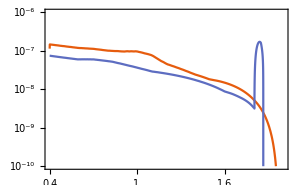

```mathematica
plottheme = "Scientific";
scalingfunctions = {"Linear", "Log"};
plotrange = {{0.4,2}, {1*10^-10,1*10^-6}};
imagesize={300,Automatic};
plotpoints=5000;
ticksx=Table[i,{i,0.4,2.,0.2}];
ticksy={{10^-10,"10^-10"},{10^-9,"10^-9"},{10^-8,"10^-8"},{10^-7,"10^-7"},{10^-6,"10^-6"}};
frameticks={{ticksy,None},{ticksx,Automatic}};
colours={pltcolors[[1]],pltcolors[[2]],pltcolors[[3]]};
framelabel={xlabel,ylabel};
plotlegends=Placed[LineLegend[Join[Table[{colours[[i]]},{i,1,Length@colours-1}],{Null}],Table[legends[[i]],{i,1,Length@legends-1}],Spacings->0.1,LegendLayout->{"Column",1},LegendMarkerSize->12],{0.675,0.825}];
bg=Plot[{Null,Null},{n,0.5,2},PlotTheme->plottheme,ScalingFunctions->scalingfunctions,PlotPoints->plotpoints,ImageSize->imagesize,PlotRange->plotrange,FrameTicks->frameticks,PlotStyle->colours,PlotLegends->plotlegends,FrameLabel->framelabel];
plote=Plot[bre[d431,n],{n,0.4,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->200,PlotStyle->colours[[1]]];
plotmu=Plot[brmu[d431,n],{n,0.4,1.8},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->200,PlotStyle->colours[[2]]];
plotmuaux=Plot[brmu[d431,n],{n,1.8,2},ScalingFunctions->scalingfunctions,PlotRange->plotrange,PlotPoints->5000,PlotStyle->colours[[2]]];
plotexp=Show[bg,plote,plotmu,plotmuaux]
Export["/home/sane/mainhnlchain/hnlchain/paperHNL/plots/br431.pdf",plotexp];
```

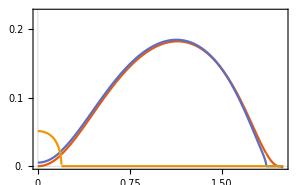

```mathematica
plottheme = "Scientific";
scalingfunctions = {"Linear", "Linear"};
plotrange = {{0,2}, {0,0.225}};
imagesize={300,Automatic};
plotpoints=5000;
ticksx=Automatic;
ticksy=Table[{i,ToString[i]},{i,0,0.2,0.05}];
frameticks={{ticksy,None},{ticksx,Automatic}};
colours={pltcolors[[1]],pltcolors[[2]],pltcolors[[3]]};
framelabel={xlabel,ylabel};
plotlegends=Placed[LineLegend[Join[Table[{colours[[i]]},{i,1,Length@colours}],{Null}],Table[legends[[i]],{i,1,Length@legends}],Spacings->0.1,LegendLayout->{"Column",1},LegendMarkerSize->12],{0.2,0.8}];
bg=Plot[{Null,Null},{n,0,2},PlotTheme->plottheme,ScalingFunctions->scalingfunctions,PlotPoints->plotpoints,ImageSize->imagesize,PlotRange->plotrange,FrameTicks->frameticks,PlotStyle->colours,PlotLegends->plotlegends,FrameLabel->framelabel];
plote=Plot[brtoy[d431,e,n],{n,0,2},ScalingFunctions->scalingfunctions,PlotRange->All,PlotPoints->200,PlotStyle->colours[[1]]];
plotmu=Plot[brtoy[d431,mu,n],{n,0,2},ScalingFunctions->scalingfunctions,PlotRange->All,PlotPoints->200,PlotStyle->colours[[2]]];
plottau=Plot[brtoy[d431,tau,n],{n,0,2},ScalingFunctions->scalingfunctions,PlotRange->All,PlotPoints->200,PlotStyle->colours[[3]]];
plotexp=Show[bg,plote,plotmu,plottau]
Export["/home/sane/mainhnlchain/hnlchain/paperHNL/plots/brtoy431.pdf",plotexp];
```

```mathematica
k321[[2]]+tau
```

2.27054

## Semileptonic Scalar Bondarenko (pp 26, 38) [411]D+ -> [-311]K0bar [421]D0 -> [-321]K- [431]Ds -> [221]eta [431]Ds -> [331]eta’

```mathematica
z[meson1_,meson2_,q2_]:=Module[{tp,t0},
tp=(meson1[[2]]+meson2[[2]])^2;
t0=(meson1[[2]]+meson2[[2]])(√meson1[[2]]-√meson2[[2]])^2;
(√(tp-q2)-√(tp-t0))/(√(tp-q2)+√(tp-t0))];
```

```mathematica
lambda[a_,b_,c_]:=a^2+b^2+c^2-2a*b-2a*c-2b*c;
```

```mathematica
fp[meson1_,meson2_,q2_]:=Module[
{f0, c, P},
If[(meson1[[5]]==411||meson1[[5]]==421)&& (meson2[[5]]==321||meson2[[5]]==311),
f0=0.7647; c=0.066; P=0.224];
If[(meson1[[5]]==411||meson1[[5]]==421)&& meson2[[5]]==211,
f0=0.6117; c=1.985; P=0.1314];
If[meson1[[5]]≠431,
1/(1-P*q2)*(f0-c(z[meson1,meson2,q2]-z[meson1,meson2,0])(1+(z[meson1,meson2,q2]+z[meson1,meson2,0])/2)),
0.495/((1-q2/2.1121^2)(1-(0.198*q2)/2.1121^2))]
];
```

```mathematica
f0[meson1_,meson2_,q2_]:=Module[
{f0, c, P},
If[(Abs[meson1[[5]]]==411||Abs[meson1[[5]]]==421)&& (Abs[meson2[[5]]]==321||Abs[meson2[[5]]]==311),
f0=0.7647; c=2.084; P=0];
If[(Abs[meson1[[5]]]==411||Abs[meson1[[5]]]==421)&& Abs[meson2[[5]]]==211,
f0=0.6117; c=1.188; P=0.0342];
If[Abs[meson1[[5]]]≠431,
1/(1-P*q2)*(f0-c(z[meson1,meson2,q2]-z[meson1,meson2,0])(1+(z[meson1,meson2,q2]+z[meson1,meson2,0])/2)),
0.495/((1-q2/2.1121^2)(1-(0.198*q2)/2.1121^2))]
];
```

```mathematica
Lambda[meson1_,meson2_,l_,n_,xi_]:=√lambda[1,(meson2[[2]]/meson1[[2]])^2,xi]*√lambda[xi,(n/meson1[[2]])^2,(l/meson1[[2]])^2];
gminus[meson1_,meson2_,l_,n_,xi_]:=xi*((n/meson1[[2]])^2+(l/meson1[[2]])^2)-((n/meson1[[2]])^2-(l/meson1[[2]])^2)^2;
```

```mathematica
ip1[meson1_,meson2_,l_,n_]:=If[n<meson1[[2]]-meson2[[2]]-l,
NIntegrate[1/(3 xi^3)*fp[meson1,meson2,xi*meson1[[2]]^2]^2*Lambda[meson1,meson2,l,n,xi]^3,{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0];
```

```mathematica
ip2[meson1_,meson2_,l_,n_]:=If[n<meson1[[2]]-meson2[[2]]-l,
NIntegrate[1/(2 xi^3)*fp[meson1,meson2,xi*meson1[[2]]^2]^2*Lambda[meson1,meson2,l,n,xi]*gminus[meson1,meson2,l,n,xi]*lambda[1,(meson2[[2]]/meson1[[2]])^2,xi],{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0];
```

```mathematica
ip3[meson1_,meson2_,l_,n_]:=If[n<meson1[[2]]-meson2[[2]]-l,
NIntegrate[1/(2 xi^3)*f0[meson1,meson2,meson1[[2]]^2*xi]^2*Lambda[meson1,meson2,l,n,xi]*gminus[meson1,meson2,l,n,xi]*(1-(meson2[[2]]/meson1[[2]])^2)^2,{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0];
```

```mathematica
width3body[meson1_,meson2_,l_,n_,u_]:=Module[{ck},
If[meson2[[5]]==211,ck=1/(√2),ck=1];
If[n<meson1[[2]]-meson2[[2]]-l,
Re[(gf^2 meson1[[2]]^5)/(64 Pi^3)*ck^2*ckm[[2,2]]^2 u^2(ip1[meson1,meson2,l,n]+ip2[meson1,meson2,l,n]+ip3[meson1,meson2,l,n])],
0]
];
```

```mathematica
width3body[d411,k311,tau,1,1]
```

0

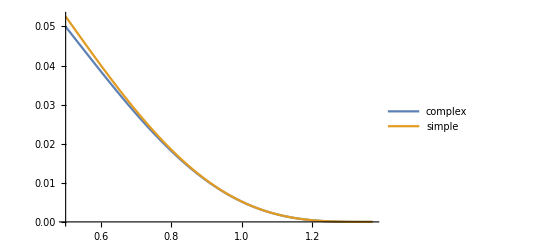

```mathematica
Plot[{width3body[d411,k311,e,n,1]/(d411[[1]]^-1+width3body[d411,k311,e,n,1]),d411[[1]]*width3body[d411,k311,e,n,1]},{n,0.5,d411[[2]]-k311[[2]]-e},PlotLegends->{"complex","simple"}]
```

```mathematica
d431[[1]]*width2body[d431,e,0.5,1]
d431[[1]]*width2body[d431,mu,0.5,1]
d431[[1]]*width3body[d431,eta221,e,0.5,1]
d431[[1]]*width3body[d431,eta331,e,0.5,1]
```

0.110003

0.11551

0.0176353

0.00237589

## Semileptonic Vector Bondarenko (pp 26, 38) [411]D+ -> [-313]Kbar*(892)0 [421]D0 -> [-323]K*(892)- [431]Ds -> [333]phi(1020)

```mathematica
vhh[q2_]:=1.03/((1-q2/2.1121^2)(1-0.27*q2/2.1121^2));
ahh0[q2_]:=0.76/((1-q2/1.96827^2)(1-0.17*q2/2.1121^2));
ahh1[q2_]:=0.66/(1-0.30*q2/2.1121^2-0.20*q2^2/2.1121^4);
ahh2[q2_]:=0.49/(1-0.67*q2/2.1121^2-0.16*q2^2/2.1121^4);
```

```mathematica
(* 431->333 (2004) Aliev et al *)
ahh1phi[q2_]:=0.54/(1-1.57*q2/d431[[2]]^2+0.16*(q2/d431[[2]]^2)^2);
ahh2phi[q2_]:=0.57/(1-4.7*q2/d431[[2]]^2+5.96*(q2/d431[[2]]^2)^2);
ahh0phi[q2_]:=0.53/(1-0.64*q2/d431[[2]]^2+2.13*(q2/d431[[2]]^2)^2);
vhhphi[q2_]:=0.64/(1-2.81*q2/d431[[2]]^2+1.34*(q2/d431[[2]]^2)^2);
```

```mathematica
ghh[meson1_,meson2_,q2_]:=If[meson1[[5]]==431&&meson2[[5]]==333,
	vhhphi[q2]/(meson1[[2]]+meson2[[2]]),
	vhh[q2]/(meson1[[2]]+meson2[[2]])];
fhh[meson1_,meson2_,q2_]:=If[meson1[[5]]==431&&meson2[[5]]==333,
	ahh1phi[q2](meson1[[2]]+meson2[[2]]),
	ahh1[q2](meson1[[2]]+meson2[[2]])];
ahhp[meson1_,meson2_,q2_]:=If[meson1[[5]]==431&&meson2[[5]]==333,
	-ahh2phi[q2]/(meson1[[2]]+meson2[[2]]),
	-ahh2[q2]/(meson1[[2]]+meson2[[2]])];
ahhm[meson1_,meson2_,q2_]:=If[meson1[[5]]==431&&meson2[[5]]==333,
	1/q2*(ahh0phi[q2]*2meson2[[2]]-fhh[meson1,meson2,q2]-(meson1[[2]]^2-meson2[[2]]^2)ahhp[meson1,meson2,q2]),
	1/q2*(ahh0[q2]*2meson2[[2]]-fhh[meson1,meson2,q2]-(meson1[[2]]^2-meson2[[2]]^2)ahhp[meson1,meson2,q2])];
```

```mathematica
F[meson1_,meson2_,l_,n_,xi_]:=(1-xi)^2-2(meson2[[2]]/meson1[[2]])^2(1+xi)+(meson2[[2]]/meson1[[2]])^4;
gplus[meson1_,meson2_,l_,n_,xi_]:=xi((n/meson1[[2]])^2+(l/meson1[[2]])^2)+((n/meson1[[2]])^2-(l/meson1[[2]])^2)^2
```

```mathematica
ivg2[meson1_,meson2_,l_,n_]:=Module[{},
If[n<meson1[[2]]-meson2[[2]]-l,1/3 meson1[[2]]^2(meson2[[2]]/meson1[[2]])^2 NIntegrate[1/xi^2 ghh[meson1,meson2,meson1[[2]]^2*xi]^2 Lambda[meson1,meson2,l,n,xi]*F[meson1,meson2,l,n,xi]*(2 xi^2-gminus[meson1,meson2,l,n,xi]),{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0]
];
```

```mathematica
ivf2[meson1_,meson2_,l_,n_]:=Module[{},
If[n<meson1[[2]]-meson2[[2]]-l,
1/(24 meson1[[2]]^2)NIntegrate[1/xi^3 fhh[meson1,meson2,meson1[[2]]^2*xi]^2*Lambda[meson1,meson2,l,n,xi]*(3F[meson1,meson2,l,n,xi](xi^2-((l/meson1[[2]])^2-(n/meson1[[2]])^2)^2)-Lambda[meson1,meson2,l,n,xi]^2+12(meson2[[2]]/meson1[[2]])^2*xi*(2 xi^2-gplus[meson1,meson2,l,n,xi])),{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0]];
```

```mathematica
ivap2[meson1_,meson2_,l_,n_]:=Module[{},
If[n<meson1[[2]]-meson2[[2]]-l,
meson1[[2]]^2/24 NIntegrate[1/xi^3 ahhp[meson1,meson2,meson1[[2]]^2*xi]^2*Lambda[meson1,meson2,l,n,xi]*F[meson1,meson2,l,n,xi]*(F[meson1,meson2,l,n,xi](2 xi^2-gplus[meson1,meson2,l,n,xi])+3gminus[meson1,meson2,l,n,xi](1-(meson2[[2]]/meson1[[2]])^2)^2),{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0]];
```

```mathematica
ivam2[meson1_,meson2_,l_,n_]:=Module[{},
If[n<meson1[[2]]-meson2[[2]]-l,
meson1[[2]]^2/8 NIntegrate[1/xi ahhm[meson1,meson2,meson1[[2]]^2*xi]^2 Lambda[meson1,meson2,l,n,xi]*F[meson1,meson2,l,n,xi]*gminus[meson1,meson2,l,n,xi],{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0]];
```

```mathematica
ivfap[meson1_,meson2_,l_,n_]:=Module[{},
If[n<meson1[[2]]-meson2[[2]]-l,
1/12 NIntegrate[1/xi^3 fhh[meson1,meson2,meson1[[2]]^2*xi]*ahhp[meson1,meson2,meson1[[2]]^2*xi]*Lambda[meson1,meson2,l,n,xi]*(3*xi*F[meson1,meson2,l,n,xi]*gminus[meson1,meson2,l,n,xi]+(1-xi-(meson2[[2]]/meson1[[2]])^2)(3F[meson1,meson2,l,n,xi](xi^2-((l/meson1[[2]])^2-(n/meson1[[2]])^2)^2)-Lambda[meson1,meson2,l,n,xi]^2)),{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0]];
```

```mathematica
ivfam[meson1_,meson2_,l_,n_]:=Module[{},
If[n<meson1[[2]]-meson2[[2]]-l,
1/4 NIntegrate[1/xi^2 fhh[meson1,meson2,meson1[[2]]^2*xi]*ahhm[meson1,meson2,meson1[[2]]^2*xi]*Lambda[meson1,meson2,l,n,xi]*F[meson1,meson2,l,n,xi]*gminus[meson1,meson2,l,n,xi],{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0]];
```

```mathematica
ivapam[meson1_,meson2_,l_,n_]:=Module[{},
If[n<meson1[[2]]-meson2[[2]]-l,
meson1[[2]]^2/4 NIntegrate[1/xi^2 ahhp[meson1,meson2,meson1[[2]]^2*xi]*ahhm[meson1,meson2,meson1[[2]]^2*xi]*Lambda[meson1,meson2,l,n,xi]*F[meson1,meson2,l,n,xi]*gminus[meson1,meson2,l,n,xi]*(1-(meson2[[2]]/meson1[[2]])^2),{xi,(l/meson1[[2]]+n/meson1[[2]])^2,(1-meson2[[2]]/meson1[[2]])^2}],
0]];
```

```mathematica
ivall[meson1_,meson2_,l_,n_]:=ivg2[meson1,meson2,l,n]+ivf2[meson1,meson2,l,n]+ivap2[meson1,meson2,l,n]+ivam2[meson1,meson2,l,n]+ivfap[meson1,meson2,l,n]+ivfam[meson1,meson2,l,n]+ivapam[meson1,meson2,l,n];
```

```mathematica
width3bodyv[meson1_,meson2_,l_,n_,u_]:=Module[{ck=1},
If[n<meson1[[2]]-meson2[[2]]-l,
Re[(gf^2 meson1[[2]]^7)/(64 Pi^3 meson2[[2]]^2)*ck^2*ckm[[2,2]]^2 u^2 ivall[meson1,meson2,l,n]],
0]
];
```

## 3body decay implementation

```mathematica
d411k311e[n_,u_]:=width3body[d411,k311,e,n,u];
d411k311mu[n_,u_]:=width3body[d411,k311,mu,n,u];
d411k313bare[n_,u_]:=width3bodyv[d411,k313,e,n,u];
d411k313barmu[n_,u_]:=width3bodyv[d411,k313,mu,n,u];

d421k321e[n_,u_]:=width3body[d421,k321,e,n,u];
d421k321mu[n_,u_]:=width3body[d421,k321,mu,n,u];
d421k323e[n_,u_]:=width3bodyv[d421,k323,e,n,u];
d421k323mu[n_,u_]:=width3bodyv[d421,k323,mu,n,u];

d431eta221e[n_,u_]:=width3body[d431,eta221,e,n,u];
d431eta221mu[n_,u_]:=width3body[d431,eta221,mu,n,u];
d431eta331e[n_,u_]:=width3body[d431,eta331,e,n,u];
d431eta331mu[n_,u_]:=width3body[d431,eta331,mu,n,u];
d431phi333e[n_,u_]:=width3bodyv[d431,phi1020,e,n,u];
d431phi333mu[n_,u_]:=width3bodyv[d431,phi1020,mu,n,u];
```

```mathematica
newwidth2hnl[meson_,n_,mixe_,mixmu_,mixtau_]:=
Switch[meson[[5]],
411,
	Re[
	width2body[meson,e,n,mixe]
	+width2body[meson,mu,n,mixmu]
	+width2body[meson,tau,n,mixtau]
	+d411k311e[n,mixe]
	+d411k311mu[n,mixmu]
	+d411k313bare[n,mixe]
	+d411k313barmu[n,mixmu]],
431,
	Re[
	width2body[meson,e,n,mixe]
	+width2body[meson,mu,n,mixmu]
	+width2body[meson,tau,n,mixtau]
	+d431eta221e[n,mixe]
	+d431eta221mu[n,mixmu]
	+d431eta331e[n,mixe]
	+d431eta331mu[n,mixmu]
	+d431phi333e[n,mixe]
	+d431phi333mu[n,mixmu]],
421,
	Re[
	d421k321e[n,mixe]
	+d421k321mu[n,mixmu]
	+d421k323e[n,mixe]
	+d421k323mu[n,mixmu]
	]
];
```

```mathematica
newwidth[meson_,n_,mixe_,mixmu_,mixtau_]:=
Re[1/meson[[1]]+newwidth2hnl[meson,n,mixe,mixmu,mixtau]];
```

```mathematica
{1/d411[[1]],newwidth[d411,1,1,0,1],newwidth[d411,1,1,1,1]}
{1/d431[[1]],newwidth[d431,1,1,0,1],newwidth[d431,1,1,1,1]}
{1/d421[[1]],newwidth[d421,1,1,0,1],newwidth[d421,1,1,1,1]}
```

{6.32883×10^-13,6.47177×10^-13,6.61075×10^-13}

{1.30595×10^-12,1.67131×10^-12,2.04202×10^-12}

{1.60497×10^-12,1.60822×10^-12,1.6109×10^-12}

```mathematica
d431[[1]]*d431eta221e[0.0001,1]
```

0.0253464

## Backup

```mathematica
d03toy[md0,mk,e,0.3]
```

0.23322

```mathematica
NIntegrate
```

```mathematica
n=0.05;
l=e;
h=mk;
Re[Integrate[Integrate[fmd[x]^2(x(n^2+l^2)-(n^2-l^2)^2)+2fpd[x]fmd[x](n^2(2 md0^2-2 h^2-4y*md0-l^2+n^2+x)+l^2(4y*md0+l^2-n^2-x))+fpd[x]^2((4y*md0+l^2-n^2-x)(2 md0^2-2 h^2-4y*md0-l^2+n^2+x)-(2 md0^2+2 h^2-x)(x-n^2-l^2)),{x,(l+n)^2,(md0-h)^2}],{y,n,(md0^2+n^2-(l+h)^2)/(2md0)}]]
```

-1.10123

```mathematica
d03[h_,l_,n_]:=NIntegrate[fmd[x]^2(x(n^2+l^2)-(n^2-l^2)^2)+2fpd[x]fmd[x](n^2(2 md0^2-2 h^2-4y*md0-l^2+n^2+x)+l^2(4y*md0+l^2-n^2-x))*fpd[x]^2((4y*mk+l^2-n^2-x)(2 mk^2-2 mpi^2-4y*mk-l^2+n^2+x)-(2 mk^2+2 mpi^2-x)(x-n^2-l^2)),{x,(l+n)^2,(md0-h)^2},{y,n,(md0^2+n^2-(l+h)^2)/(2md0)}]
```

```mathematica
Length
```

```mathematica
ds2[l_,n_]:=(1-n^2/mds^2+2 l^2/mds^2+l^2/n^2(1-l^2/mds^2))√((1+n^2/mds^2-l^2/mds^2)^2-4*n^2/mds^2);
```

```mathematica
ds2[me,1]*356*10^-12
```

1.95897×10^-10

```mathematica
d03toy[h1_,h2_,l_,n_]:=factor*
NIntegrate[
fmd[x]^2(x(n^2+l^2)-(n^2-l^2)^2)
+2fpd[x]*fmd[x](n^2(2 h1^2-2 h2^2-4y*h1-l^2+n^2+x)
+l^2(4y*h1+l^2-n^2-x))
+fpd[x]^2((4y*h1+l^2-n^2-x)(2 h1^2-2 h2^2-4y*h1-l^2+n^2+x)
-(2 h1^2+2 h2^2-x)(x-n^2-l^2))
,{x,(l+n)^2,(h1-h2)^2},{y,n,(x-l^2-n^2)/(2l)},Method->"GlobalAdaptive"];
```